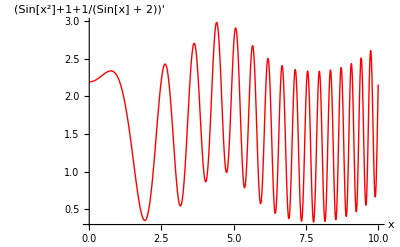

```mathematica
(* Priklad c. 1 *)

fce[x_]:=Sin[x^2]+1+1/(Sin[x]+2);
fced[x_]:=D[fce[x]];

Plot[fced[√(t^2+1)],{t,0,10},AxesLabel->{"x","(Sin[x^2]+1+1/(Sin[x] + 2))'"},PlotStyle->{Thick,Red}]
```

```mathematica
(* Priklad c. 2 *)
rce=3*x^2+4*x+6==0;
vyraz=√x;
vys=Solve[rce, {x}];
```

```mathematica
vyraz/.vys[[2]]
```

√(1/3 (-2+ⅈ √14))

```mathematica
(* Priklad c. 3 *)
```

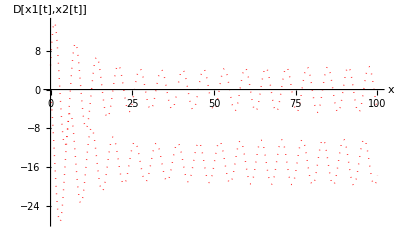

```mathematica
soustavaRovnic={x1'[t]-x2[t]==-Pi/30*x1[t]+15,x1[t]+x2'[t]==0.5*Sin[t]};
soustavaPodminek={x1[0]==5,x2[0]==-1};
nezndif={x1[t],x2[t]};

vys=NDSolve[{soustavaRovnic,soustavaPodminek},{nezndif},{t,0,100}];
Plot[{x1[t],x2[t]}/.vys,{t,0,100}, PlotStyle->{Red,Thick,Dotted},AxesLabel->{"x","D[x1[t],x2[t]]"}]
```